# QCD calculation: Webber et al. Sec. 7 (with FeynRules)

## Two-jet cross sections (Only QCD; mass ignored) again

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.4 (7 Jun 2016)

by Thomas Hahn

### FeynRules model files

```mathematica
model = FileNameJoin[{NotebookDirectory[],"models","SM","Standard_Model_FA","Standard_Model_FA"}]
```

/Users/misho/.ghq/github.com/misho104/FeynLecture/models/SM/Standard_Model_FA/Standard_Model_FA

You can check whether the files exist or not by:

```mathematica
FileExistsQ[model<>".mod"]
FileExistsQ[model<>".gen"]
```

True

True

### Create Topology (and also ignore helicities)

```mathematica
topologies=CreateTopologies[0,2->2];
_Hel=0;
```

### u c → u c

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]},
GenericModel->model,
Model->model
];
Paint[diag]
```

loading generic model file /Users/misho/.ghq/github.com/misho104/FeynLecture/models/SM/Standard_Model_FA/Standard_Model_FA.gen

> $GenericMixing is OFF

generic model {/Users/misho/.ghq/github.com/misho104/FeynLecture/models/SM/Standard_Model_FA/Standard_Model_FA} initialized

loading classes model file /Users/misho/.ghq/github.com/misho104/FeynLecture/models/SM/Standard_Model_FA/Standard_Model_FA.mod

> 43 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 93 vertices

classes model {/Users/misho/.ghq/github.com/misho104/FeynLecture/models/SM/Standard_Model_FA/Standard_Model_FA} initialized

Excluding 0 Generic, 7 Classes, and 7 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 7 Classes, and 7 Particles fields

in total: 0 Classes insertions

Paint::nolevel: Warning: Level \!\(\*RowBox[{"Classes"}]\) is not contained in this insertion.

FeynArtsGraphics[{u,c}→{u,c}][]

FeynArtsGraphics[{u,c}→{u,c}][]

This is wrong.
In a different model, particles have different labels, and parameters have different names.
We have to check the model file (.mod) to see which particle is which.

In this model, gluon is labelled as V[3]. So we should not “Exclude” V[3].

Excluding 0 Generic, 4 Classes, and 4 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 4 Classes, and 4 Particles fields

in total: 1 Classes insertion

> Top. 1: 1 diagram

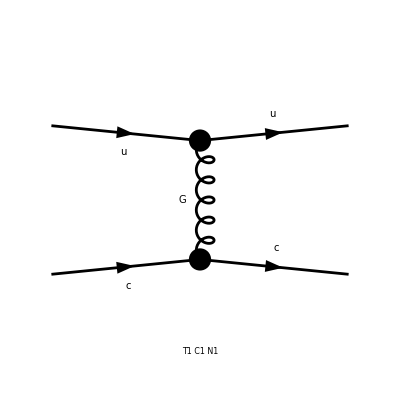

```mathematica
diag=InsertFields[topologies,{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],V[1],V[2]},
GenericModel->model,
Model->model
];
Paint[diag];
```

```mathematica
(* Remember the prefactor 4/9 *)
ClearProcess[];
amp = CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA]
matrixelement = FullSimplify[4/9 SquaredME[amp]//.HelicityME[amp]//.ColourME[amp]]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[3,{1,Col1}],k[1],MU,{(2 Q)/3}},{F[3,{2,Col2}],k[2],MC,{(2 Q)/3}}}→{{F[3,{1,Col3}],k[3],MU,{(2 Q)/3}},{F[3,{2,Col4}],k[4],MC,{(2 Q)/3}}}][1/2 gc84^2 Den[T,0] Mat[F1 SUN1]-1/2 gc84^2 Den[T,0] Mat[F2 SUN1]+1/4 gc84^2 Den[T,0] Mat[F3 SUN1]-1/4 gc84^2 Den[T,0] Mat[F4 SUN1]-1/6 gc84^2 Den[T,0] Mat[F1 SUN2]+1/6 gc84^2 Den[T,0] Mat[F2 SUN2]-1/12 gc84^2 Den[T,0] Mat[F3 SUN2]+1/12 gc84^2 Den[T,0] Mat[F4 SUN2]]

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

2/9 (4 MC2^2+4 MU2^2+T^2+(S-U)^2+2 MC2 (4 MU2-S+T-U)-2 MU2 (S-T+U)) Abs[gc84]^4 Den[T,0]^2

```mathematica
matrixelement//.{MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}
```

(2 (T^2+(S-U)^2) Abs[gc84]^4)/(9 T^2)

Here we see a unknown parameter.
The interpretation is stored in M$FACouplings.

```mathematica
M$FACouplings
```

{gc11→-EL,gc12→EL,gc13→-EL,gc15→EL,gc18→-EL,gc19→-(cw EL)/sw,gc21→(cw EL)/sw,gc23→-EL,gc26→EL,gc27→(cw EL)/sw,gc29→-(cw EL)/sw,gc31→(cw EL)/sw,gc33→-(cw EL)/sw,gc35→GS,gc36→-GS,gc37→-4 Alfas π,gc38L[e1x2_,e2x2_]→IndexSum[CKMC[e2x2,Generation$1] (yd[Generation$1,e1x2]Superscript[*]),{Generation$1,1,3}],gc38R[e1x2_,e2x2_]→-IndexSum[CKMC[Generation$1,e1x2] yu[Generation$1,e2x2],{Generation$1,1,3}],gc39L[e1x2_,e2x2_]→-(yd[e2x2,e1x2]Superscript[*])/(√2),gc39R[e1x2_,e2x2_]→yd[e1x2,e2x2]/(√2),gc40L[e1x2_,e2x2_]→-(yd[e2x2,e1x2]Superscript[*])/(√2),gc40R[e1x2_,e2x2_]→-yd[e1x2,e2x2]/(√2),gc41[e1x2_,e2x2_]→yl[e2x2,e1x2]Superscript[*],gc42L[e1x2_,e2x2_]→-(yl[e2x2,e1x2]Superscript[*])/(√2),gc42R[e1x2_,e2x2_]→yl[e1x2,e2x2]/(√2),gc43L[e1x2_,e2x2_]→-(yl[e2x2,e1x2]Superscript[*])/(√2),gc43R[e1x2_,e2x2_]→-yl[e1x2,e2x2]/(√2),gc44L[e1x2_,e2x2_]→IndexSum[CKM[Generation$1,e2x2] (yu[Generation$1,e1x2]Superscript[*]),{Generation$1,1,3}],gc44R[e1x2_,e2x2_]→-IndexSum[CKM[e1x2,Generation$1] yd[Generation$1,e2x2],{Generation$1,1,3}],gc45L[e1x2_,e2x2_]→(yu[e2x2,e1x2]Superscript[*])/(√2),gc45R[e1x2_,e2x2_]→-yu[e1x2,e2x2]/(√2),gc46L[e1x2_,e2x2_]→-(yu[e2x2,e1x2]Superscript[*])/(√2),gc46R[e1x2_,e2x2_]→-yu[e1x2,e2x2]/(√2),gc50→EL/(2 sw),gc51→-EL/(2 sw),gc52→EL,gc56→-EL/(2 sw),gc57→-EL/(2 sw),gc62→-4 Alfa π,gc63→(cw EL)/sw,gc64→(4 Alfa π)/sw^2,gc65R[e1x2_,e2x2_]→-yl[e1x2,e2x2],gc67→-(EL (cw^2+sw^2))/(2 cw sw),gc68→-(cw EL)/(2 sw)+(EL sw)/(2 cw),gc75→(4 Alfa cw π)/sw,gc80→-(4 Alfa cw^2 π)/sw^2,gc81→-EL,gc82→(2 EL)/3,gc83→-EL/3,gc84→GS,gc85→GS,gc86[e1x2_,e2x2_]→(EL CKM[e1x2,e2x2])/(√2 sw),gc87[e1x2_,e2x2_]→(EL CKMC[e2x2,e1x2])/(√2 sw),gc88→EL/(√2 sw),gc89→EL/(√2 sw),gc90L→(cw EL)/(2 sw)-(EL sw)/(6 cw),gc90R→-(2 EL sw)/(3 cw),gc91L→-(EL (3 cw^2+sw^2))/(6 cw sw),gc91R→(EL sw)/(3 cw),gc92→(EL (cw^2+sw^2))/(2 cw sw),gc93L→-(EL (cw^2-sw^2))/(2 cw sw),gc93R→(EL sw)/cw}

```mathematica
matrixelement //. M$FACouplings //. {MC2->0,MU2->0,Den[a_,b_]:>1/(a-b)}
```

(2 (T^2+(S-U)^2) Abs[GS]^4)/(9 T^2)

This result is the same as we saw in Lecture1-4.nb.